```mathematica
EllipticX[ξ_,ε_,λ_,αϵ_]:=NIntegrate[(λ+(αϵ ε)/(1-2/ξξ))/(√(ε^2-(1+λ^2/ξξ^2) (1-2/ξξ)-(αϵ^2+2 αϵ ε λ)/ξξ^2) (αϵ^2/(1-2/ξξ)+ξξ^2)),{ξξ,ξ,Infinity},Method->"DoubleExponential",(*WorkingPrecision->$MachinePrecision,*)WorkingPrecision->128] (* F. obliczająca wartości referencyjne *)
```

```mathematica
dat=Import["E:\\temp\\download\\data.csv"]; (* Wartości obliczone *)
```

```mathematica
ref=Table[EllipticX@@dat[[ii,1;;4]],{ii,2,Length[dat]}]; (* Wartości "dokładne" (arbitrary precision) *)
```

```mathematica
dat[[1]]
```

{ξ,ε,λ,α,Result (Julia),Time (Julia),Result (Mathematica),Time (Mathematica),Difference in results,Difference in time (minus sign means Julia is faster)}

```mathematica
dat[[2]]
```

{84,15,4,0,0.00318158,4.82×10^-7,0.0031816,0.002318,-2.56077×10^-8,-0.00231752}

```mathematica
(dat[[2;;,7]]/ref-1)/$MachineEpsilon (* Błąd względny w jednostkach $MachineEpsilon *)
```

{0.,1.,1.,-0.5,-0.5,-1.,-0.5,1.,-1.,0.,0.,-0.5,-71003.,-0.5,-71018.,2.,0.,-0.5,1.,0.,-0.5,-827.,1.,-0.5,1.,-1.,0.,83.,-0.5,0.,-6.5,-0.5,-1.,-1.,0.,0.,1.,0.,0.,1.,-0.5,0.,0.,-1.,-1.,0.,0.,-0.5,0.,-1.5,-1.,0.,0.,-3.5,0.,-1.,0.,-0.5,-0.5,-784.5,1.,1.,-70955.5,0.,-0.5,-2.,-0.5,-0.5,-1.,-1.,-1.,-0.5,13.,1.,-1.5,-0.5,-0.5,-692.,-693.5,-1.,0.,-3.,0.,-1.5,-1045.5,0.,0.,-0.5,-1.5,1.,-69976.5,-0.5,0.,-1.,-1.5,-1.}

```mathematica
(dat[[2;;,5]]/ref-1)/$MachineEpsilon (* W jednostkach $MachineEpsilon błędy są gigantyczne *)
```

{-3.62481×10^10,-4.78331×10^10,1.24176×10^10,-2.87171×10^10,-3.28337×10^10,-1.13809×10^10,-268.5,7.57648×10^8,-4.64986×10^10,1270.,-4.22077×10^7,-3.83362×10^10,-71002.,-71057.,3.47253×10^9,15.,-3.1417×10^10,-4.71004×10^10,-4.28543×10^10,3543.,-4.5147×10^10,-828.,-3.62421×10^10,-4.60537×10^10,-4.67743×10^10,-3.14727×10^10,-2.67669×10^7,3.44634×10^9,1.48393×10^7,-2.82833×10^13,4.35523×10^7,1.55046×10^7,-65555.5,-2.28065×10^10,-68031.,-3.9992×10^10,-4.8627×10^9,-1.99893×10^10,4.10484×10^6,3534.,-3.62288×10^10,-4.60491×10^10,5.69859×10^9,-4.02114×10^10,6055.,-2.68295×10^7,-4.15074×10^10,1274.,-4.77622×10^10,-4.60447×10^10,-62408.5,-1.55998×10^10,-3.38928×10^8,3.68983×10^8,-8.89947×10^7,-2.59126×10^10,-4.00132×10^10,-4.60443×10^10,-4.33541×10^10,-784.5,8846.,7.64699×10^8,-70956.5,-546.,144.,-2.87666×10^6,-4.64847×10^10,-2.81709×10^13,-62381.5,-2.44622×10^10,159.,-4.60115×10^10,13.,-544.5,-1.34571×10^10,-1.25519×10^10,-4.60396×10^10,-693.,4.47597×10^9,-58368.,7.26205×10^6,-4.44507×10^8,1959.,-66435.5,-1046.,5.70862×10^6,-268.5,64.,-2.21905×10^10,-2.82796×10^13,-69976.5,-2.21941×10^10,-4.75701×10^10,5.70087×10^9,-4.45982×10^10,-4.15134×10^10}

```mathematica
dat[[2;;,8]]/dat[[2;;,6]]//MinMax (* Przyspieszenie obliczeń *)
```

{566.34,6838.16}

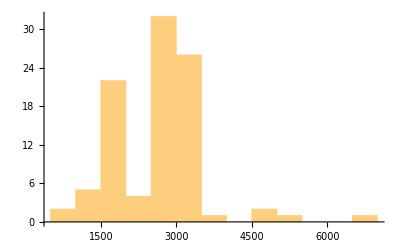

```mathematica
dat[[2;;,8]]/dat[[2;;,6]]//Histogram (* Rozkład prawdopodobnieństwa przyspiszenia *)
```